## The RGB Cube corners.

```mathematica
<<ToMatlab`
```

```mathematica
Clear[θ]
```

```mathematica
MatrixForm[TrigFactor[YABCube[θ]]]
```

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | ((-1)^(1/3) ((-1+(-1)^(1/3)) Cos[θ]+(ⅈ+(-1)^(5/6)) Sin[θ]))/(√6) | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | ((-1)^(5/6) (-ⅈ+(-1)^(1/6)) ((ⅈ+(-1)^(1/6)) Cos[θ]-(-1)^(1/3) Sin[θ]))/(√6) | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

```mathematica
cubeCorners[minMax_]:={{minMax[[1,1]],minMax[[1,2]],minMax[[1,2]],minMax[[1,1]],minMax[[1,1]],minMax[[1,1]],minMax[[1,2]],minMax[[1,2]]},{minMax[[2,1]],minMax[[2,1]],minMax[[2,2]],minMax[[2,2]],minMax[[2,2]],minMax[[2,1]],minMax[[2,1]],minMax[[2,2]]},{minMax[[3,1]],minMax[[3,1]],minMax[[3,1]],minMax[[3,1]],minMax[[3,2]],minMax[[3,2]],minMax[[3,2]],minMax[[3,2]]}};
```

```mathematica
YABCube[θ_] := cubeCorners[YABAxisRanges[θ]];
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
```

```mathematica
RGBAxisRanges = {{0,1},{0,1},{0,1}};
RGBCube = cubeCorners[RGBAxisRanges];
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
```

```mathematica
MatrixForm[YABCube[θ]]
```

(0 | √3 | √3 | 0 | 0 | 0 | √3 | √3
-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | -Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6) | -Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | -Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6) | Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6)
-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | -Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | -Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | -Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6) | Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6))

```mathematica
MatrixForm[RGBCube]
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
Map[Max,faces]
```

{4,8,7,8,8,6}

```mathematica
RGBCube3D[corners_]:=Module[{RGBCube,faces,ranges},
ranges =Transpose[{ Map[Min,corners],Map[Max,corners]}];Graphics3D[{Polygon[corners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[1]]]]]]],Polygon[corners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[2]]]]]]],Polygon[corners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[3]]]]]]],Polygon[corners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[4]]]]]]],Polygon[corners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[5]]]]]]],Polygon[corners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[6]]]]]]]},Lighting->"Neutral",PlotRange->{{ranges[[1,1]],ranges[[1,2]]},{ranges[[2,1]],ranges[[2,2]]},{ranges[[3,1]],ranges[[3,2]]}},Axes->True]
]
```

```mathematica
YABCube3D[θ_]:=Module[{corners,RGBCube,faces,ranges},corners = Transpose[YABCube[θ]];RGBCube = {{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}};
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
ranges = YABAxisRanges[θ];Graphics3D[{Polygon[corners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[1]]]]]]],Polygon[corners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[2]]]]]]],Polygon[corners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[3]]]]]]],Polygon[corners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[4]]]]]]],Polygon[corners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[5]]]]]]],Polygon[corners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[6]]]]]]]},Lighting->"Neutral",PlotRange->{{ranges[[1,1]],ranges[[1,2]]},{ranges[[2,1]],ranges[[2,2]]},{ranges[[3,1]],ranges[[3,2]]}},Axes->True]
]
```

```mathematica
Transpose[cubeCorners[ YABAxisRanges[θ]]]
```

{{0,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{√3,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{√3,-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{0,-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6),Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6)},{0,-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)},{0,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)},{√3,Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)},{√3,1,-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)}}

```mathematica
iYAB[θ]. YABCubeCorners
```

```mathematica
YABCube3D[θ_]:=Module[{RGBinYABcorners,RGBCubeCorners,YABCubeCorners,YABinRGBCubeCorners,faces,ranges},
RGBinYABcorners = Transpose[YABCube[θ]];
RGBCubeCorners = Transpose[cubeCorners[{{0,1},{0,1},{0,1}}]];YABCubeCorners =Transpose[cubeCorners[ YABAxisRanges[θ]]];
YABinRGBCubeCorners =Transpose[cubeCorners[ iYAB[θ]. cubeCorners[ YABAxisRanges[θ]]]];
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}};
ranges = YABAxisRanges[θ];Graphics3D[{Opacity[0.9],
Polygon[RGBinYABcorners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[1]]]]]]],Polygon[RGBinYABcorners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[2]]]]]]],Polygon[RGBinYABcorners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[3]]]]]]],Polygon[RGBinYABcorners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[4]]]]]]],Polygon[RGBinYABcorners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[5]]]]]]],Polygon[RGBinYABcorners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[RGBCubeCorners[[faces[[6]]]]]]],
Opacity[0.2],
Polygon[YABCubeCorners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[1]]]]]]],Polygon[YABCubeCorners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[2]]]]]]],Polygon[YABCubeCorners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[3]]]]]]],Polygon[YABCubeCorners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[4]]]]]]],Polygon[YABCubeCorners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[5]]]]]]],Polygon[YABCubeCorners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[YABinRGBCubeCorners[[faces[[6]]]]]]]},Lighting->"Neutral",PlotRange->YABAxisRanges[θ],Axes->True]
]
```

## Rotation Matrices

```mathematica
RotationMatrixX[α_]:={{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}};
RotationMatrixY[β_]:={{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}};
RotationMatrixZ[γ_]:={{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}};
R=Function[{α,β, γ},Evaluate[TrigFactor[RotationMatrixX[α].RotationMatrixZ[γ].RotationMatrixY[β]]]];
MatrixForm[R[α,β, γ]]
```

(Cos[β] Cos[γ] | Sin[γ] | -Cos[γ] Sin[β]
1/4 (2 Cos[α-β]-2 Cos[α+β]+Sin[α-β-γ]+Sin[α+β-γ]-Sin[α-β+γ]-Sin[α+β+γ]) | Cos[α] Cos[γ] | 1/4 (-Cos[α-β-γ]+Cos[α+β-γ]+Cos[α-β+γ]-Cos[α+β+γ]+2 Sin[α-β]+2 Sin[α+β])
1/4 (Cos[α-β-γ]+Cos[α+β-γ]-Cos[α-β+γ]-Cos[α+β+γ]-2 Sin[α-β]+2 Sin[α+β]) | -Cos[γ] Sin[α] | 1/4 (2 Cos[α-β]+2 Cos[α+β]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ]))

Solution for the Yab cube. Luminocity axis is in the X value.

```mathematica
YAB=Function[{θ},Evaluate[TrigFactor[RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]]]];
iYAB=Function[{θ},Evaluate[TrigFactor[RotationMatrixY[Pi/4].RotationMatrixZ[-ArcTan[1/Sqrt[2]]].RotationMatrixX[-θ]]]];
YABCube=Function[{θ},Evaluate[TrigFactor[FullSimplify[TrigToExp[YAB[θ].RGBCube]]]]];
```

```mathematica
Print[MatrixForm[YAB[θ]].MatrixForm[RGBCube],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[YAB[θ]. RGBCube]]],1]]
Print[MatrixForm[iYAB[θ]].MatrixForm[YABCube[θ]],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[iYAB[θ]. YABCube[θ]]]],1]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

(1/(√3) | -√(2/3) Sin[π/6+θ] | -√(2/3) Cos[π/6+θ]
1/(√3) | √(2/3) Cos[θ] | -√(2/3) Sin[θ]
1/(√3) | -√(2/3) Sin[π/6-θ] | √(2/3) Cos[π/6-θ]).(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)=(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

The inverse of a rotation is equal to the transpose of the rotation matrix

```mathematica
TrigFactor[FullSimplify[TrigToExp[Inverse[YAB[θ]]]]] == Transpose[YAB[θ]]
```

True

```mathematica
Manipulate[Show[YABCube3D[θ],Graphics3D[{Opacity[0.5],ranges = YABAxisRanges[θ];Cuboid[0.9{{ranges[[1,1]],ranges[[2,1]],ranges[[3,1]]},{ranges[[1,2]],ranges[[2,2]],ranges[[3,2]]}}]}]],{θ,0,Pi}]
```

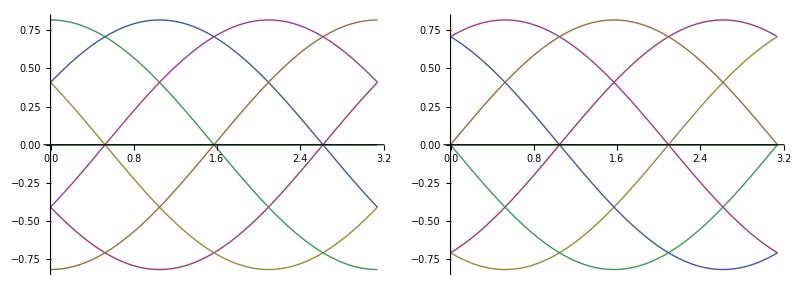

```mathematica
Grid[{{Plot[Evaluate[YABCube[θ][[2]]], {θ, 0, Pi}],Plot[Evaluate[YABCube[θ][[3]]], {θ, 0, Pi}]}}]
```

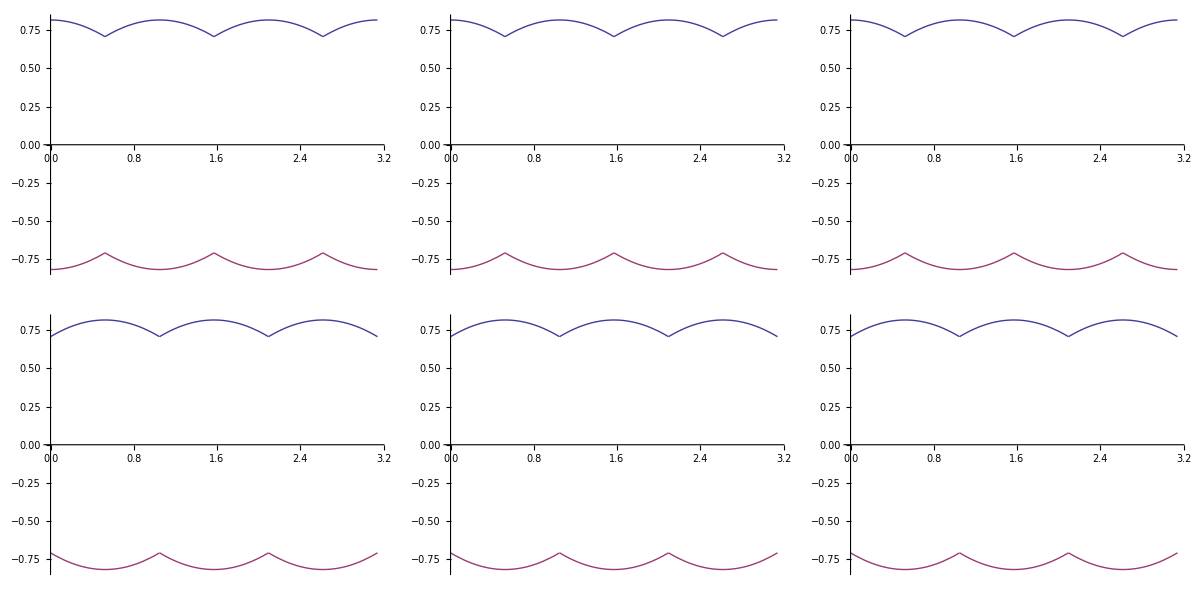

```mathematica
Grid[{{Plot[{Max[YABCube[θ ][[2]]],Min[YABCube[θ ][[2]]]},{θ,0,Pi}],Plot[{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{θ,0,Pi}],Plot[{√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]] ,-√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]]},{θ,0,Pi}]},{Plot[{Max[YABCube[θ ][[3]]],Min[YABCube[θ ][[3]]]},{θ,0,Pi}], Plot[{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)},{θ,0,Pi}],Plot[{√(2/3) Cos[π/6-Mod[θ,Pi/3]] ,-√(2/3) Cos[π/6-Mod[θ,Pi/3]]},{θ,0,Pi}]}}]
```

```mathematica
YABPolygon[θ_]:=Transpose[{Take[YABCube[θ ][[2]],{2,7}],Take[YABCube[θ ][[3]],{2,7}]}]
```

```mathematica
Manipulate[Graphics[{Black,Rectangle[Sequence@@Transpose[{YABAxisRanges[θ ][[2]],YABAxisRanges[θ ][[3]]}]],Blue,Polygon[YABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-√(2/3) ,√(2/3) },{-√(2/3) ,√(2/3) }}],{θ,0,Pi}]
```

```mathematica
YABAxisRanges[θ_]:={{0,Sqrt[3]},{-√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]] ,√(2/3) Cos[π/6-Mod[θ -Pi/6,Pi/3]]},{-√(2/3) Cos[π/6-Mod[θ,Pi/3]] ,√(2/3) Cos[π/6-Mod[θ,Pi/3]]}};
YABAxisLengths = Function[{θ},Evaluate[Flatten[YABAxisRanges[θ][[All,2]] - YABAxisRanges[θ][[All,1]]]]];
scaleVec = Function[{θ},Evaluate[Simplify[1/YABAxisLengths[θ]]]];
```

```mathematica
Print["L[θ] = ",MatrixForm[YABAxisLengths[θ]]," = ",MatrixForm[TrigExpand[YABAxisLengths[θ]]]," = ",MatrixForm[FullSimplify[TrigExpand[YABAxisLengths[θ]]]]]
Print["s[θ] = ",MatrixForm[scaleVec[θ]]," = ",MatrixForm[TrigExpand[scaleVec[θ]]]," = ",MatrixForm[FullSimplify[TrigExpand[scaleVec[θ]]]]]
```

L[θ] = (√3
2 √(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]
2 √(2/3) Cos[π/6-Mod[θ,π/3]]) = (√3
√2 Cos[Mod[-π/6+θ,π/3]]+√(2/3) Sin[Mod[-π/6+θ,π/3]]
√2 Cos[Mod[θ,π/3]]+√(2/3) Sin[Mod[θ,π/3]]) = (√3
√2 Cos[Mod[π/6+θ,π/3]]+√(2/3) Sin[Mod[π/6+θ,π/3]]
√2 Cos[Mod[θ,π/3]]+√(2/3) Sin[Mod[θ,π/3]])

s[θ] = (1/(√3)
1/2 √(3/2) Sec[1/6 (π-6 Mod[-π/6+θ,π/3])]
1/2 √(3/2) Sec[1/6 (π-6 Mod[θ,π/3])]) = (1/(√3)
(√6)/(2 √3 Cos[Mod[-π/6+θ,π/3]]+2 Sin[Mod[-π/6+θ,π/3]])
(√6)/(2 √3 Cos[Mod[θ,π/3]]+2 Sin[Mod[θ,π/3]])) = (1/(√3)
(√(3/2))/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])
(√(3/2))/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]))

```mathematica
scaleMatrix= Function[{θ},Evaluate[{{scaleVec[θ][[1]],0,0},{0,scaleVec[θ][[2]],0},{0,0,scaleVec[θ][[3]]}}]];
nYAB= Function[{θ},Evaluate[TrigReduce[FullSimplify[TrigExpand[scaleMatrix[θ]. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]]]]]];
inYAB= Function[{θ},Evaluate[Inverse[nYAB[θ]]]];
MatrixForm[scaleMatrix[θ]]
MatrixForm[nYAB[θ]]
MatrixForm[TrigReduce[FullSimplify[TrigExpand[nYAB[θ]. RGBCube]]]]
```

(1/(√3) | 0 | 0
0 | 1/2 √(3/2) Sec[1/6 (π-6 Mod[-π/6+θ,π/3])] | 0
0 | 0 | 1/2 √(3/2) Sec[1/6 (π-6 Mod[θ,π/3])])

(1/3 | 1/3 | 1/3
(-Cos[θ]-√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | Cos[θ]/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]) | (-Cos[θ]+√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]))
(-√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | -Sin[θ]/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]) | (√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])))

(0 | 1/3 | 2/3 | 1/3 | 2/3 | 1/3 | 2/3 | 1
0 | (-Cos[θ]-√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | (Cos[θ]-√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | Cos[θ]/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]) | (Cos[θ]+√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | (-Cos[θ]+√3 Sin[θ])/(2 (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]])) | -Cos[θ]/(√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]) | 0
0 | (-√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | (-√3 Cos[θ]-Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | -Sin[θ]/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]) | (√3 Cos[θ]-Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | (√3 Cos[θ]+Sin[θ])/(2 (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])) | Sin[θ]/(√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]]) | 0)

```mathematica
Manipulate[MatrixForm[FullSimplify[nYAB[θ]. RGBCube]],{θ,0,Pi}]
```

```mathematica
nYABCube= Function[{θ},Evaluate[FullSimplify[nYAB[θ].RGBCube]]];
```

```mathematica
nYABPolygon= Function[{θ},Evaluate[Transpose[{Take[nYABCube[θ ][[2]],{2,7}],Take[nYABCube[θ ][[3]],{2,7}]}]]];
```

```mathematica
Manipulate[LxyAxisRanges = Simplify[YABAxisRanges[θ ]];Grid[{{Graphics[{Black,Rectangle[Sequence@@Transpose[{LxyAxisRanges[[2]],LxyAxisRanges[[3]]}]],Blue,Polygon[nYABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-1/2,1/2},{-1/2 ,1/2}}],MatrixForm[{Row[{" θ = ",θ}],Row[{LxyAxisRanges[[1,1]],"< L < ",LxyAxisRanges[[1,2]]}], Row[{LxyAxisRanges[[2,1]],"< x < ",LxyAxisRanges[[2,2]]}],Row[{LxyAxisRanges[[3,1]],"< y < ",LxyAxisRanges[[3,2]]}]}]}}],{θ,0,Pi}]
```

## Discrete Representation of the rotation

We have a source which makes discrete steps of 1/srcRange the question is to what degree of precision do we need to represent the transformation given that we require a precision of 1/wrkRange. What is required is the smallest number which can result from the transformation of a unit cube!

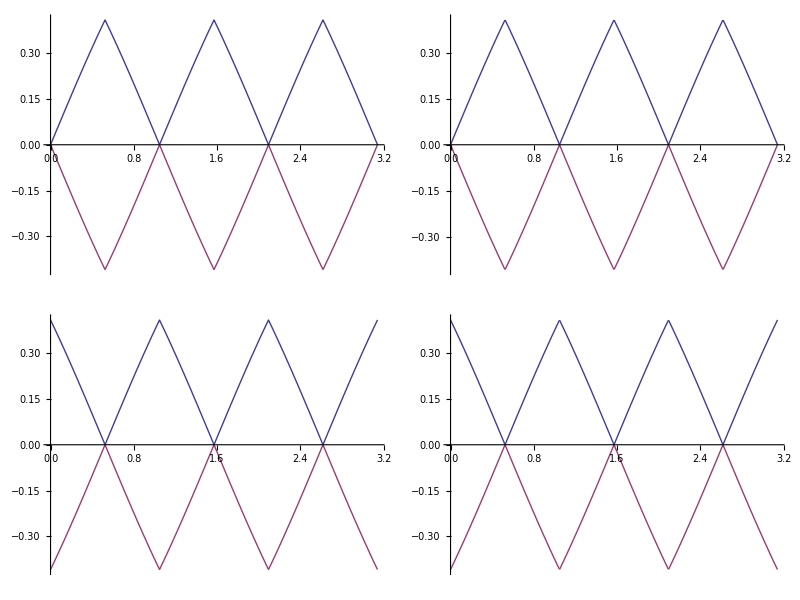

```mathematica
Grid[{{Plot[{Min[Abs[YABCube[θ ][[3,{2,3,4,5,6,7}]]]],-Min[Abs[YABCube[θ ][[3,{2,3,4,5,6,7}]]]]},{θ,0,Pi}], Plot[{√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]]},{θ,0,Pi}]},{Plot[{Min[Abs[YABCube[θ ][[2,{2,3,4,5,6,7}]]]],-Min[Abs[YABCube[θ ][[2,{2,3,4,5,6,7}]]]]},{θ,0,Pi}],Plot[{√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]]},{θ,0,Pi}]}}]
```

```mathematica
Manipulate[{MatrixForm[N[d[YAB[θ],srcRange]]- N[YAB[θ]]],MatrixForm[N[YAB[θ]]]},{θ,0,Pi},{srcRange,1,255,1}]
```

```mathematica
]
```

```mathematica
MatrixForm[YAB[θ].{1,1,1}]
```

(√3
0
0)

```mathematica
MatrixForm[Map[Solve[{#1==0,-Pi ≤θ ≤Pi},θ]&,YAB[θ],{2}]]
```

({} | {} | {}
{{θ→-π/6},{θ→(5 π)/6}} | {{θ→-π/2},{θ→π/2}} | {{θ→-(5 π)/6},{θ→π/6}}
{{θ→-(2 π)/3},{θ→π/3}} | {{θ→0},{θ→-π},{θ→π}} | {{θ→-π/3},{θ→(2 π)/3}})

```mathematica
maskPos[θ_]:=Evaluate[Map[Reduce[{#1>0,0 ≤θ <2Pi},θ]&,YAB[θ],{2}]]
maskNeg[θ_]:=Evaluate[Map[Reduce[{#1<0,0 ≤θ <2Pi},θ]&,YAB[θ],{2}]]
MatrixForm[maskPos[θ]]
MatrixForm[maskNeg[θ]]
```

(0≤θ<2 π | 0≤θ<2 π | 0≤θ<2 π
(5 π)/6<θ<(11 π)/6 | 0≤θ<π/2||(3 π)/2<θ<2 π | π/6<θ<(7 π)/6
π/3<θ<(4 π)/3 | π<θ<2 π | 0≤θ<(2 π)/3||(5 π)/3<θ<2 π)

(False | False | False
0≤θ<(5 π)/6||(11 π)/6<θ<2 π | π/2<θ<(3 π)/2 | 0≤θ<π/6||(7 π)/6<θ<2 π
0≤θ<π/3||(4 π)/3<θ<2 π | 0<θ<π | (2 π)/3<θ<(5 π)/3)

```mathematica
Manipulate[{MatrixForm[MatrixForm[maskPos[θ]]]},{θ,0,2 Pi}]
```

```mathematica
δYABpos[θ_]:=Evaluate[MapThread[Piecewise[{{0,#2},{#3,#1}},0]&,{maskPos[θ],maskNeg[θ],YAB[θ]},2]]
δYABneg[θ_]:=Evaluate[MapThread[Piecewise[{{0,#1},{#3,#2}},0]&,{maskPos[θ],maskNeg[θ],YAB[θ]},2]]
MatrixForm[δYABpos[θ]]
MatrixForm[δYABneg[θ]]
```

(Piecewise[{{1/(√3), 0≤θ<2 π}, {0, True}}] | Piecewise[{{1/(√3), 0≤θ<2 π}, {0, True}}] | Piecewise[{{1/(√3), 0≤θ<2 π}, {0, True}}]
Piecewise[{{0, 0≤θ<(5 π)/6||(11 π)/6<θ<2 π}, {-√(2/3) Sin[π/6+θ], (5 π)/6<θ<(11 π)/6}, {0, True}}] | Piecewise[{{0, π/2<θ<(3 π)/2}, {√(2/3) Cos[θ], 0≤θ<π/2||(3 π)/2<θ<2 π}, {0, True}}] | Piecewise[{{0, 0≤θ<π/6||(7 π)/6<θ<2 π}, {-√(2/3) Sin[π/6-θ], π/6<θ<(7 π)/6}, {0, True}}]
Piecewise[{{0, 0≤θ<π/3||(4 π)/3<θ<2 π}, {-√(2/3) Cos[π/6+θ], π/3<θ<(4 π)/3}, {0, True}}] | Piecewise[{{0, 0<θ<π}, {-√(2/3) Sin[θ], π<θ<2 π}, {0, True}}] | Piecewise[{{0, (2 π)/3<θ<(5 π)/3}, {√(2/3) Cos[π/6-θ], 0≤θ<(2 π)/3||(5 π)/3<θ<2 π}, {0, True}}])

(0 | 0 | 0
Piecewise[{{0, (5 π)/6<θ<(11 π)/6}, {-√(2/3) Sin[π/6+θ], 0≤θ<(5 π)/6||(11 π)/6<θ<2 π}, {0, True}}] | Piecewise[{{0, 0≤θ<π/2||(3 π)/2<θ<2 π}, {√(2/3) Cos[θ], π/2<θ<(3 π)/2}, {0, True}}] | Piecewise[{{0, π/6<θ<(7 π)/6}, {-√(2/3) Sin[π/6-θ], 0≤θ<π/6||(7 π)/6<θ<2 π}, {0, True}}]
Piecewise[{{0, π/3<θ<(4 π)/3}, {-√(2/3) Cos[π/6+θ], 0≤θ<π/3||(4 π)/3<θ<2 π}, {0, True}}] | Piecewise[{{0, π<θ<2 π}, {-√(2/3) Sin[θ], 0<θ<π}, {0, True}}] | Piecewise[{{0, 0≤θ<(2 π)/3||(5 π)/3<θ<2 π}, {√(2/3) Cos[π/6-θ], (2 π)/3<θ<(5 π)/3}, {0, True}}])

```mathematica
MatrixForm[PiecewiseExpand[δYABpos[θ]]]
MatrixForm[PiecewiseExpand[δYABneg[θ]]]
```

Piecewise[{{{{0,0,0},{0,0,0},{0,0,0}}, θ≥2 π||θ<0}, {{{1/(√3),1/(√3),1/(√3)},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, (2 π)/3≤θ≤(5 π)/6}, {{{1/(√3),1/(√3),1/(√3)},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π/2≤θ<(2 π)/3}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],0},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, 0≤θ≤π/6}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, (11 π)/6≤θ<2 π}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π/6<θ≤π/3}, {{{1/(√3),1/(√3),1/(√3)},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π/3<θ<π/2}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{0,-√(2/3) Sin[θ],0}}, (4 π)/3≤θ≤(3 π)/2}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, (7 π)/6≤θ<(4 π)/3}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, (5 π)/6<θ≤π}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, π<θ<(7 π)/6}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],0}}, (3 π)/2<θ≤(5 π)/3}, {{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, True}}]

Piecewise[{{{{0,0,0},{0,0,0},{0,0,0}}, θ≥2 π||θ<0}, {{{0,0,0},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, (5 π)/3≤θ≤(11 π)/6}, {{{0,0,0},{0,0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, (3 π)/2≤θ<(5 π)/3}, {{{0,0,0},{0,√(2/3) Cos[θ],0},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, π≤θ≤(7 π)/6}, {{{0,0,0},{0,√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, (5 π)/6≤θ<π}, {{{0,0,0},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{0,0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, (7 π)/6<θ≤(4 π)/3}, {{{0,0,0},{0,√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,Cos[θ]/(√2)+Sin[θ]/(√6)}}, (4 π)/3<θ<(3 π)/2}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{0,-√(2/3) Sin[θ],0}}, π/3≤θ≤π/2}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,0},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, π/6≤θ<π/3}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),0,0}}, θ==0||(11 π)/6<θ<2 π}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),0,-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],0}}, 0<θ<π/6}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],0}}, π/2<θ≤(2 π)/3}, {{{0,0,0},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],0},{0,-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}, True}}]

```mathematica
MatrixForm[PiecewiseExpand[δYABpos[θ].{1,1,1}]]
MatrixForm[PiecewiseExpand[δYABneg[θ].{1,1,1}]]
```

Piecewise[{{{0,0,0}, θ≥2 π||θ<0}, {{√3,-√(2/3) Cos[θ],-Cos[θ]/(√2)+Sin[θ]/(√6)}, (5 π)/6<θ≤π}, {{√3,-√(2/3) Cos[θ],-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, π<θ<(7 π)/6}, {{√3,√(2/3) Cos[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}, 0≤θ≤π/6}, {{√3,√(2/3) Cos[θ],Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (11 π)/6≤θ<2 π}, {{√3,-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, (4 π)/3≤θ≤(3 π)/2}, {{√3,-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (7 π)/6≤θ<(4 π)/3}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, (3 π)/2<θ≤(5 π)/3}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (5 π)/3<θ<(11 π)/6}, {{√3,-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, π/2≤θ<(2 π)/3}, {{√3,-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6)}, (2 π)/3≤θ≤(5 π)/6}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, π/3<θ<π/2}, {{√3,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),Cos[θ]/(√2)+Sin[θ]/(√6)}, True}}]

Piecewise[{{{0,0,0}, θ≥2 π||θ<0}, {{0,-√(2/3) Cos[θ],-Cos[θ]/(√2)+Sin[θ]/(√6)}, θ==0||(11 π)/6<θ<2 π}, {{0,-√(2/3) Cos[θ],-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, 0<θ<π/6}, {{0,√(2/3) Cos[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}, π≤θ≤(7 π)/6}, {{0,√(2/3) Cos[θ],Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (5 π)/6≤θ<π}, {{0,-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, π/3≤θ≤π/2}, {{0,-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, π/6≤θ<π/3}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[θ]}, π/2<θ≤(2 π)/3}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)-Sin[θ]/(√2),Cos[θ]/(√2)-√(2/3) Sin[θ]+Sin[θ]/(√6)}, (2 π)/3<θ<(5 π)/6}, {{0,-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, (3 π)/2≤θ<(5 π)/3}, {{0,-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6)}, (5 π)/3≤θ≤(11 π)/6}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[θ]}, (4 π)/3<θ<(3 π)/2}, {{0,√(2/3) Cos[θ]-Cos[θ]/(√6)+Sin[θ]/(√2),Cos[θ]/(√2)+Sin[θ]/(√6)}, True}}]

```mathematica
{1,2,3}[[All]]
```

{1,2,3}

```mathematica
δYABExtrema[θ_,form_,idx_]:=FullSimplify[PiecewiseExpand[matrixForm[Map[max,Transpose[{δYABpos[θ].{1,1,1},-δYABneg[θ].{1,1,1}}]][[idx]]]]]/.{max->Max,matrixForm->form}
δYABExtrema[θ,MatrixForm,All]
```

Piecewise[{{(0
0
0), θ≥2 π||θ<0}, {(√3
-√(2/3) Cos[θ]
Max[-√(2/3) Cos[π/6+θ],-Cos[θ]/(√2)+Sin[θ]/(√6)]), (5 π)/6<θ≤π}, {(√3
-√(2/3) Cos[θ]
-(√3 Cos[θ]+Sin[θ])/(√6)), π<θ<(7 π)/6}, {(√3
√(2/3) Cos[θ]
(√3 Cos[θ]+Sin[θ])/(√6)), θ≥0&&6 θ≤π}, {(√3
√(2/3) Cos[θ]
Max[√(2/3) Cos[π/6+θ],Cos[θ]/(√2)-Sin[θ]/(√6)]), (11 π)/6≤θ<2 π}, {(√3
Max[√(2/3) Sin[1/6 (π-6 θ)],Cos[θ]/(√6)-Sin[θ]/(√2)]
-√(2/3) Sin[θ]), (3 π)/2<θ≤(5 π)/3}, {(√3
Max[√(2/3) Sin[1/6 (π-6 θ)],Cos[θ]/(√6)-Sin[θ]/(√2)]
Max[√(2/3) Cos[π/6+θ],Cos[θ]/(√2)-Sin[θ]/(√6)]), (5 π)/3<θ<(11 π)/6}, {(√3
-Cos[θ]/(√6)+Sin[θ]/(√2)
Max[-√(2/3) Cos[π/6+θ],-Cos[θ]/(√2)+Sin[θ]/(√6)]), (2 π)/3≤θ≤(5 π)/6}, {(√3
-Cos[θ]/(√6)+Sin[θ]/(√2)
√(2/3) Sin[θ]), π/2≤θ<(2 π)/3}, {(√3
Max[Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[π/6+θ]]
√(2/3) Sin[θ]), π/3<θ<π/2}, {(√3
Max[Cos[θ]/(√6)+Sin[θ]/(√2),√(2/3) Sin[π/6+θ]]
(√3 Cos[θ]+Sin[θ])/(√6)), π/6<θ≤π/3}, {(√3
Max[-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[π/6+θ]]
-√(2/3) Sin[θ]), (4 π)/3≤θ≤(3 π)/2}, {(√3
Max[-Cos[θ]/(√6)-Sin[θ]/(√2),-√(2/3) Sin[π/6+θ]]
-(√3 Cos[θ]+Sin[θ])/(√6)), True}}]

```mathematica
δYABExtrema[θ,MatrixForm,1]
```

Piecewise[{{0, θ≥2 π||θ<0}, {√3, True}}]

```mathematica
δYABExtrema[θ,MatrixForm,2]
```

Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Cos[θ], (5 π)/6≤θ≤(7 π)/6}, {√(2/3) Cos[θ], (θ≥0&&6 θ≤π)||(11 π)/6≤θ<2 π}, {-Cos[θ]/(√6)-Sin[θ]/(√2), (7 π)/6<θ≤(3 π)/2}, {Cos[θ]/(√6)-Sin[θ]/(√2), (3 π)/2<θ<(11 π)/6}, {-Cos[θ]/(√6)+Sin[θ]/(√2), π/2≤θ<(5 π)/6}, {Cos[θ]/(√6)+Sin[θ]/(√2), True}}]

```mathematica
δYABExtrema[θ,MatrixForm,3]
δYABExtrema[θ,MatrixForm,3]
```

Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Sin[θ], (4 π)/3≤θ≤(5 π)/3}, {√(2/3) Sin[θ], π/3≤θ≤(2 π)/3}, {-Cos[θ]/(√2)+Sin[θ]/(√6), (2 π)/3<θ≤π}, {Cos[θ]/(√2)+Sin[θ]/(√6), θ≥0&&3 θ<π}, {-Cos[θ]/(√2)-Sin[θ]/(√6), π<θ<(4 π)/3}, {Cos[θ]/(√2)-Sin[θ]/(√6), True}}]

```mathematica
Evaluate[{δYABExtrema[θ,StandardForm,1],δYABExtrema[θ,StandardForm,2],δYABExtrema[θ,StandardForm,3]}]
```

{Piecewise[{{0, θ≥2 π||θ<0}, {√3, True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Cos[θ], (5 π)/6≤θ≤(7 π)/6}, {√(2/3) Cos[θ], (θ≥0&&6 θ≤π)||(11 π)/6≤θ<2 π}, {-Cos[θ]/(√6)-Sin[θ]/(√2), (7 π)/6<θ≤(3 π)/2}, {Cos[θ]/(√6)-Sin[θ]/(√2), (3 π)/2<θ<(11 π)/6}, {-Cos[θ]/(√6)+Sin[θ]/(√2), π/2≤θ<(5 π)/6}, {Cos[θ]/(√6)+Sin[θ]/(√2), True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Sin[θ], (4 π)/3≤θ≤(5 π)/3}, {√(2/3) Sin[θ], π/3≤θ≤(2 π)/3}, {-Cos[θ]/(√2)+Sin[θ]/(√6), (2 π)/3<θ≤π}, {Cos[θ]/(√2)+Sin[θ]/(√6), θ≥0&&3 θ<π}, {-Cos[θ]/(√2)-Sin[θ]/(√6), π<θ<(4 π)/3}, {Cos[θ]/(√2)-Sin[θ]/(√6), True}}]}

```mathematica
δYABExtrema[0.2,StandardForm,2]
```

0.800221

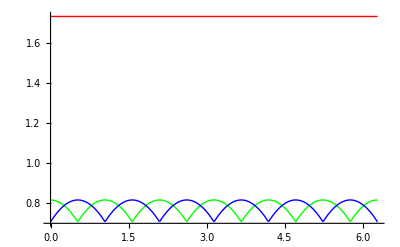

```mathematica
Plot[{Piecewise[{{0, θ≥2 π||θ<0}, {√3, True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Cos[θ], (5 π)/6≤θ≤(7 π)/6}, {√(2/3) Cos[θ], (θ≥0&&6 θ≤π)||(11 π)/6≤θ<2 π}, {-Cos[θ]/(√6)-Sin[θ]/(√2), (7 π)/6<θ≤(3 π)/2}, {Cos[θ]/(√6)-Sin[θ]/(√2), (3 π)/2<θ<(11 π)/6}, {-Cos[θ]/(√6)+Sin[θ]/(√2), π/2≤θ<(5 π)/6}, {Cos[θ]/(√6)+Sin[θ]/(√2), True}}],Piecewise[{{0, θ≥2 π||θ<0}, {-√(2/3) Sin[θ], (4 π)/3≤θ≤(5 π)/3}, {√(2/3) Sin[θ], π/3≤θ≤(2 π)/3}, {-Cos[θ]/(√2)+Sin[θ]/(√6), (2 π)/3<θ≤π}, {Cos[θ]/(√2)+Sin[θ]/(√6), θ≥0&&3 θ<π}, {-Cos[θ]/(√2)-Sin[θ]/(√6), π<θ<(4 π)/3}, {Cos[θ]/(√2)-Sin[θ]/(√6), True}}]},{θ,0,2Pi},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

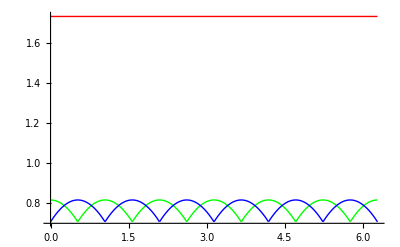

```mathematica
Plot[{√3,   √(2/3) Sin[Mod[θ-Pi/6,Pi/3]+Pi/3],√(2/3) Sin[Mod[θ,Pi/3]+Pi/3]},{θ,0,2Pi},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

```mathematica
Plot[Evaluate[{δYABExtrema[θ,StandardForm,1],δYABExtrema[θ,StandardForm,2],δYABExtrema[θ,StandardForm,3]}],{θ,0,2Pi},PlotRange->All,PlotStyle->{Red,Green,Blue}]
```

-Graphics-

```mathematica
d[src_,srcRange_]:=IntegerPart[src*srcRange]/srcRange
```

```mathematica
Manipulate[{MatrixForm[N[d[YAB[θ],tRange].RGBCube]],MatrixForm[N[YAB[θ].RGBCube]]},{{θ,-0.1537},-Pi,Pi},{tRange,1,765,1}]
```

```mathematica
Manipulate[cube=d[d[nYAB[θ],tRange].RGBCube- nYAB[θ].RGBCube,dstRange];{MatrixForm[cube  dstRange],Max[cube] dstRange,Min[cube] dstRange},{{θ,-0.1537},-Pi,Pi},{{tRange,255},1,1024,1},{{dstRange,255},1,255,1}]
```

```mathematica
Union[Flatten[YAB[θ]]]
```

{1/(√3),√(2/3) Cos[θ],-√(2/3) Sin[θ],-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6),Cos[θ]/(√2)+Sin[θ]/(√6)}

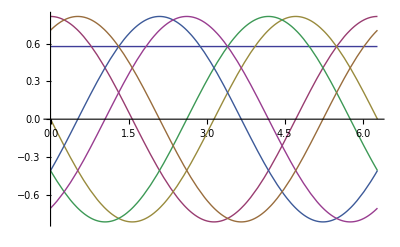

```mathematica
Plot[{1/(√3),√(2/3) Cos[θ],-√(2/3) Sin[θ],-Cos[θ]/(√6)-Sin[θ]/(√2),-Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√2)+Sin[θ]/(√6),Cos[θ]/(√2)+Sin[θ]/(√6)},{θ,0,2Pi}]
```

```mathematica
TrigReduce[-Cos[θ]/(√6)-Sin[θ]/(√2)]
MatrixForm[TrigFactor[YAB[θ]]]
```

1/6 (-√6 Cos[θ]-3 √2 Sin[θ])

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ])

```mathematica
MatrixForm[TrigFactor[YAB[θ]]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ])

```mathematica
Reduce[TrigReduce[({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}})==YAB[θ]]]
Solve[%,θ]
```

Sin[π/6-θ]==-√3 Sin[θ]+Sin[π/6+θ]&&Cos[π/6+θ]==-2 Sin[θ]+√3 Sin[π/6+θ]&&Cos[θ]==-√3 Sin[θ]+2 Sin[π/6+θ]&&Cos[π/6-θ]==-Sin[θ]+√3 Sin[π/6+θ]

{{}}

```mathematica
Manipulate[{({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[θ+π/6], √(2/3) Cos[θ], √(2/3) Sin[θ-π/6]}, {-√(2/3) Cos[θ+π/6], -√(2/3) Sin[θ], √(2/3) Cos[θ-π/6]}})==YAB[θ],Plot[{-Sin[θ+π/6]/Sin[θ],Cos[θ],Sin[θ-π/6]/Sin[θ]},{θ,0,2Pi}]},{{θ,-0.1537},-Pi,Pi}]
```

```mathematica
TrigReduce[TrigExpand[Sin[θ+π/6]/Sin[θ]]]
TrigReduce[TrigExpand[Sin[θ-π/6]/Sin[θ]]]
```

1/2 (√3+Cot[θ])

1/2 (√3-Cot[θ])

```mathematica
MatrixForm[Series[({{1, 1, 1}, {- Sin[θ+π/6], Cos[θ], Sin[θ-π/6]}, {- Cos[θ+π/6], - Sin[θ], Cos[θ-π/6]}}),{θ,0,6}]]
```

(1 | 1 | 1
-1/2-(√3 θ)/2+θ^2/4+θ^3/(4 √3)-θ^4/48-θ^5/(80 √3)+θ^6/1440+O[θ]^7 | 1-θ^2/2+θ^4/24-θ^6/720+O[θ]^7 | -1/2+(√3 θ)/2+θ^2/4-θ^3/(4 √3)-θ^4/48+θ^5/(80 √3)+θ^6/1440+O[θ]^7
-(√3)/2+θ/2+(√3 θ^2)/4-θ^3/12-θ^4/(16 √3)+θ^5/240+θ^6/(480 √3)+O[θ]^7 | -θ+θ^3/6-θ^5/120+O[θ]^7 | (√3)/2+θ/2-(√3 θ^2)/4-θ^3/12+θ^4/(16 √3)+θ^5/240-θ^6/(480 √3)+O[θ]^7)

```mathematica
rYAB[θ_]:= ({{1, 1, 1}, {- Sin[θ+π/6], Cos[θ], Sin[θ-π/6]}, {- Cos[θ+π/6], - Sin[θ], Cos[θ-π/6]}})
```

```mathematica
Manipulate[cube=d[d[rYAB[θ],tRange].RGBCube- rYAB[θ].RGBCube,dstRange];{MatrixForm[cube  dstRange],Max[cube] dstRange,Min[cube] dstRange},{{θ,-0.1537},-Pi,Pi},{{tRange,255},1,1024,1},{{dstRange,255},1,255,1}]
```

Where does this error ocure

```mathematica
δYABsign[θ_]:=Evaluate[MapThread[Piecewise[{{1,#1},{-1,#2}},0]&,{maskPos[θ],maskNeg[θ],YAB[θ]},2]]
MatrixForm[δYABsign[θ]]
```

MapThread::mptd: Object maskPos[θ] at position {2, 1} in MapThread[TagBox[GridBox[{{"{", GridBox[{{"1", "#1"}, {-1, "#2"}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]] &, {maskPos[θ], maskNeg[θ], {{1/√3, 1/√3, 1/√3}, {-√2/3\ Sin[Times[« 2 »] + θ], √2/3\ Cos[θ], -√2/3\ Sin[Times[« 2 »] + Times[« 2 »]]}, {-√2/3\ Cos[Times[« 2 »] + θ], -√2/3\ Sin[θ], √2/3\ Cos[Times[« 2 »] + Times[« 2 »]]}}}, 2] has only 0 of required 2 dimensions.

MapThread[Piecewise[{{1, #1}, {-1, #2}, {0, True}}]&,{maskPos[θ],maskNeg[θ],{{1/(√3),1/(√3),1/(√3)},{-√(2/3) Sin[π/6+θ],√(2/3) Cos[θ],-√(2/3) Sin[π/6-θ]},{-√(2/3) Cos[π/6+θ],-√(2/3) Sin[θ],√(2/3) Cos[π/6-θ]}}},2]

```mathematica
s=δYABsign[θ].{1,1,1};
```

```mathematica
MatrixForm[PiecewiseExpand[{s[[1]] δYABsign[θ][[1]],s[[2]] δYABsign[θ][[2]],s[[2]] δYABsign[θ][[2]]}]]
```

Piecewise[{{{{0,0,0},{0,0,0},{0,0,0}}, θ≥2 π||θ<0}, {{{3,3,3},{-1,1,1},{-1,1,1}}, π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {{{3,3,3},{0,0,0},{0,0,0}}, θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {{{3,3,3},{1,-1,1},{1,-1,1}}, 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {{{3,3,3},{1,1,-1},{1,1,-1}}, True}}]

```mathematica
Piecewise[{{MatrixForm[{{1,1,1},{0,0,0},{0,0,0}}], θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {MatrixForm[{{1,1,1},{-1,1,1},{-1,1,1}}], π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {MatrixForm[{{1,1,1},{0,0,0},{0,0,0}}], θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {MatrixForm[{{1,1,1},{1,-1,1},{1,-1,1}}], 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {MatrixForm[{{1,1,1},{1,1,-1},{1,1,-1}}], π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}}]
```

Piecewise[{{(1 | 1 | 1
0 | 0 | 0
0 | 0 | 0), θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {(1 | 1 | 1
-1 | 1 | 1
-1 | 1 | 1), π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {(1 | 1 | 1
0 | 0 | 0
0 | 0 | 0), θ==π/6||θ==π/2||θ==(5 π)/6||θ==(7 π)/6||θ==(3 π)/2||θ==(11 π)/6}, {(1 | 1 | 1
1 | -1 | 1
1 | -1 | 1), 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {(1 | 1 | 1
1 | 1 | -1
1 | 1 | -1), π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}, {0, True}}]

```mathematica
Piecewise[{{G+B<1,π/6<θ<π/2||(7 π)/6<θ<(3 π)/2},
{R+G<1,π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6},
{R+B<1,0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π},{False,2 π<θ<0}},Null]
```

Piecewise[{{B+G<1, π/6<θ<π/2||(7 π)/6<θ<(3 π)/2}, {G+R<1, π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6}, {B+R<1, 0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π}, {Null, True}}]

```mathematica
{π/6,π/2 ,(7 π)/6,(3 π)/2},
{π/2,(5π)/6 ,(3π)/2,(11π)/6},
{π/6,π/2,(7 π)/6,(3 π)/2}
```

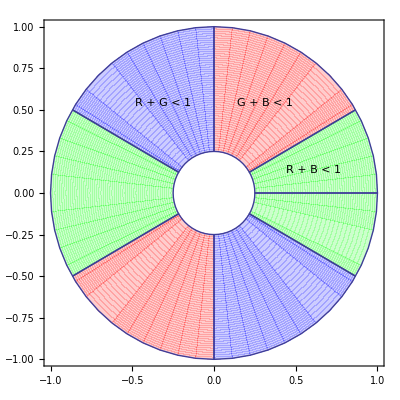

```mathematica
Show[ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2Pi},{r,1/4,1},RegionFunction->Function[{x,y,θ,r},π/6<θ<π/2||(7 π)/6<θ<(3 π)/2],Mesh->None, PlotStyle->{Red},PlotRange-> 1,PlotLegends->Placed["G + B < 1",{0.3Cos[π/3]+0.5,0.3 Sin[π/3]+0.5}],Axes->False],
ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2Pi},{r,1/4,1},RegionFunction->Function[{x,y,θ,r},π/2<θ<(5 π)/6||(3 π)/2<θ<(11 π)/6],Mesh->None, PlotStyle->{Blue},PlotRange-> 1,PlotLegends->Placed["R + G < 1",{0.3 Cos[(2 π)/3]+0.5,0.3 Sin[(2 π)/3]+0.5}],Axes->False],
ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2Pi},{r,1/4,1},RegionFunction->Function[{x,y,θ,r},0≤θ<π/6||(5 π)/6<θ<(7 π)/6||(11 π)/6<θ<2 π],Mesh->None, PlotStyle->{Green},PlotRange-> 1,PlotLegends->Placed["R + B < 1",{0.3 Cos[π/14]+0.5,0.3 Sin[π/14]+0.5}],Axes->False]]
```

```mathematica
FullSimplify[YAB[θ].{R,G,B}]
TrigReduce[%]
```

{(B+G+R)/(√3),-((B-2 G+R) Cos[θ])/(√6)+((B-R) Sin[θ])/(√2),((B-R) Cos[θ])/(√2)+((B-2 G+R) Sin[θ])/(√6)}

{(B+G+R)/(√3),1/6 (-√6 B Cos[θ]+2 √6 G Cos[θ]-√6 R Cos[θ]+3 √2 B Sin[θ]-3 √2 R Sin[θ]),1/6 (3 √2 B Cos[θ]-3 √2 R Cos[θ]+√6 B Sin[θ]-2 √6 G Sin[θ]+√6 R Sin[θ])}

```mathematica
FullSimplify[YAB[θ].{R,G,1-R}]
FullSimplify[YAB[θ].{R,G,1-G}]
FullSimplify[YAB[θ].{R,1-R,B}]
```

{(1+G)/(√3),((-1+2 G) Cos[θ])/(√6)+((1-2 R) Sin[θ])/(√2),((3-6 R) Cos[θ]+√3 (1-2 G) Sin[θ])/(3 √2)}

{(1+R)/(√3),((-1+3 G-R) Cos[θ])/(√6)-((-1+G+R) Sin[θ])/(√2),(-3 (-1+G+R) Cos[θ]+√3 (1-3 G+R) Sin[θ])/(3 √2)}

{(1+B)/(√3),-((-2+B+3 R) Cos[θ])/(√6)+((B-R) Sin[θ])/(√2),((B-R) Cos[θ])/(√2)+((-2+B+3 R) Sin[θ])/(√6)}

Apply the limits in Lxy to RGB. We have upper and lower limits on the values for Lxy. To Convert to RGB without stepping outside the cube.

```mathematica
iYAB[θ_]:=Inverse[YAB[θ]]
inYAB[θ_]:=Inverse[nYAB[θ]]
```

```mathematica
RGBPixel[L_,x_,y_,θ_]:=  TrigFactor[inYAB[θ].{L,x,y}]
```

```mathematica
Clear[RGBPixel ]
```

```mathematica
MatrixForm[FullSimplify[TrigFactor[TrigExpand[RGBPixel[L,x,y,θ]]]]]
```

(1/3 (6 L+x Cos[Mod[π/6+θ,π/3]] (√3 Cos[θ]+3 Sin[θ])+y (Cos[θ-Mod[θ,π/3]]+2 Cos[θ+Mod[θ,π/3]]-√3 Sin[θ-Mod[θ,π/3]])+x (Cos[θ]+√3 Sin[θ]) Sin[Mod[π/6+θ,π/3]])
2/3 (3 L+y Sin[θ] (√3 Cos[Mod[θ,π/3]]+Sin[Mod[θ,π/3]])-x Cos[θ] (√3 Cos[Mod[π/6+θ,π/3]]+Sin[Mod[π/6+θ,π/3]]))
1/3 (6 L+x Cos[Mod[π/6+θ,π/3]] (√3 Cos[θ]-3 Sin[θ])-y (2 Cos[θ-Mod[θ,π/3]]+Cos[θ+Mod[θ,π/3]]+√3 Sin[θ+Mod[θ,π/3]])+x (Cos[θ]-√3 Sin[θ]) Sin[Mod[π/6+θ,π/3]]))

```mathematica
Manipulate[Show[{ParametricPlot3D[{RGBPixel[L,a,-maxB,θ],RGBPixel[L,a,maxB,θ]},{L,0,1},{a,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},maxL<L<1-maxL &&-maxA< a <maxA  ],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None],ParametricPlot3D[{RGBPixel[L,-maxA,b,θ],RGBPixel[L,maxA,b,θ]},{L,0,1},{b,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},maxL<L<1-maxL &&-maxB< b <maxB  ],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None],ParametricPlot3D[{RGBPixel[maxL,a,b,θ],RGBPixel[1-maxL,a,b,θ]},{a,-0.5,0.5},{b,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},-maxA< a <maxA &&-maxB< b <maxB],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None]}],{θ,0,2 Pi},{maxL,0,1},{maxA,0,0.5},{maxB,0,0.5}]
```

```mathematica
RGBPixel[minL,maxA,-maxB,θ]
```

{0.23041,-0.753113,1.7227}

```mathematica
minL=0.2;
maxA=0.8;
maxB=0.8;
θ = 0.1;
ParametricPlot3D[{RGBPixel[L,a,-maxB,θ],RGBPixel[L,a,maxB,θ]},{L,0,1},{a,-0.5,0.5},RegionFunction->Function[{x,y,z,L,a,b},minL<L<1-minL &&-maxA< a <maxA  ],Mesh->None,BoundaryStyle->Red,PlotRange->{{0,1},{0,1},{0,1}},Axes->None]
```

-Graphics3D-

```mathematica
Chromatic Bins
```

```mathematica
MatrixForm[√6 YAB[0]]
```

(√2 | √2 | √2
-1 | 2 | -1
-√3 | 0 | √3)

```mathematica
ToMatlab[({{√3, 0, 0}, {0, √6, 0}, {0, 0, √2}}).YAB[0]]
```

[1,1,1;(-1),2,(-1);(-1),0,1];

```mathematica
Simplify[YABAxisRanges[0]]
```

{{0,√3},{-√(2/3),√(2/3)},{-1/(√2),1/(√2)}}

```mathematica
Simplify[2 √(2/3)]
```

2 √(2/3)

```mathematica
N[256 {2 √(2/3),√2}]
```

{418.046,362.039}

```mathematica
N[256 {4,2}]/N[256 {2 √(2/3),√2}]
```

{2.44949,1.41421}

## 2 D rotation Matrix

```mathematica
RotationMatrix2D[θ_]:=1/(√2 Sin[π/4+Mod[θ,Pi/2]] ){{ Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}
```

```mathematica
RotationMatrix2DScale[θ_]:=(√2 Sin[π/4+Mod[θ,Pi/2]] )
RotationMatrix2D[θ_]:={{ Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}
```

```mathematica
MatrixForm[TrigFactor[RotationMatrix2D[θ]]]
```

((-1/2-ⅈ/2) (-1)^(3/4) Cos[θ] Csc[π/4+Mod[θ,π/2]] | (-1/2-ⅈ/2) (-1)^(3/4) Csc[π/4+Mod[θ,π/2]] Sin[θ]
(1/2+ⅈ/2) (-1)^(3/4) Csc[π/4+Mod[θ,π/2]] Sin[θ] | (-1/2-ⅈ/2) (-1)^(3/4) Cos[θ] Csc[π/4+Mod[θ,π/2]])

```mathematica
minMax2D = RotationMatrix2D[θ].{{-1,-1,1,1},{-1,1,-1,1}};
```

```mathematica
minMax2D
```

{{-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2)},{-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)+(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),-(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2),(Cos[θ] Csc[π/4+Mod[θ,π/2]])/(√2)-(Csc[π/4+Mod[θ,π/2]] Sin[θ])/(√2)}}

```mathematica
Union[minMax2D[[1]]]
```

{-Cos[θ]-Sin[θ],Cos[θ]-Sin[θ],-Cos[θ]+Sin[θ],Cos[θ]+Sin[θ]}

```mathematica
InputForm[RotationMatrixX[θ].RGBCube]
```

{{0, 1, 1, 0, 0, 0, 1, 1}, {0, 0, Cos[θ], Cos[θ], Cos[θ] + Sin[θ], Sin[θ], Sin[θ], Cos[θ] + Sin[θ]}, 
 {0, 0, -Sin[θ], -Sin[θ], Cos[θ] - Sin[θ], Cos[θ], Cos[θ], Cos[θ] - Sin[θ]}}

```mathematica
TrigFactor[Union[minMax2D[[1]]]]
TrigFactor[Union[minMax2D[[2]]]]
```

{(1+ⅈ) (-1)^(3/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1+ⅈ) (-1)^(3/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]]}

{(1+ⅈ) (-1)^(3/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1+ⅈ) (-1)^(3/4) √2 Sin[π/4-θ] Sin[π/4+Mod[θ,π/2]],(1-ⅈ) (-1)^(1/4) √2 Sin[π/4+θ] Sin[π/4+Mod[θ,π/2]]}

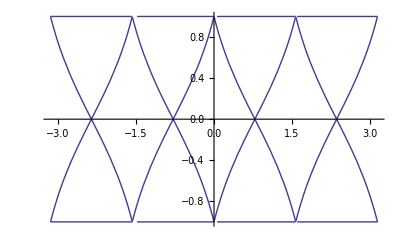

```mathematica
Plot[TrigFactor[Union[minMax2D[[1]]]],{θ,-Pi, Pi}]
```

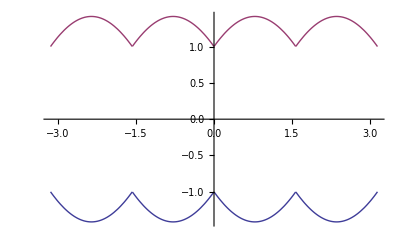

```mathematica
Plot[{-√2 Sin[π/4+Mod[θ,Pi/2]],√2 Sin[π/4+Mod[θ,Pi/2]]},{θ,-Pi, Pi}]
```

```mathematica
RotationMatrixX[θ]
```

{{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}}

```mathematica
square = {{-0.5,0.5,0.5,-0.5},{-0.5,-0.5,0.5,0.5}};
squareShift[θ_]:= {{0.5 Cos[θ],0.5 Cos[θ],0.5 Cos[θ],0.5 Cos[θ]},{0.5 Sin[-θ],0.5 Sin[-θ],0.5 Sin[-θ],0.5 Sin[-θ]}};
```

```mathematica
xyCube[θ_]:=FullSimplify[ Transpose[RotationMatrix2DScale[θ]RotationMatrix2D[θ].square +{{0.5,0.5,0.5,0.5},{0.5,0.5,0.5,0.5}} ]]
```

```mathematica
Manipulate[{θ,Sin[θ]^2,Graphics[{Blue,Polygon[xyCube[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5}]]]]],Black,Rectangle[{0,0},{1,1}]},PlotRange->{{-0.5,1.5},{-0.5 ,1.5}}]},{{θ,0},-Pi/2,Pi/2}]
```

```mathematica
YABAxisRanges[0]
```

{{0,√3},{-(√(3/2))/2-1/(2 √6),(√(3/2))/2+1/(2 √6)},{-1/(√2),1/(√2)}}

```mathematica
RotationMatrix2DScale
```

```mathematica
nYABPolygon[0]
```

{{-1/4,-1/2},{1/4,-1/2},{1/2,0},{1/4,1/2},{-1/4,1/2},{-1/2,0}}

```mathematica
RGBCube
```

{{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}}

```mathematica
xyCube[Pi/2]
```

{{0,1,0,1},{0,0,-1,-1}}

```mathematica
FullSimplify[y/Cos[θ] + (1-x-y Tan[θ])Sin[θ]]
```

y Cos[θ]+Sin[θ]-x Sin[θ]

```mathematica
FullSimplify[x/Cos[θ] + (y-x Tan[θ])Sin[θ]]
```

x Cos[θ]+y Sin[θ]

```mathematica
RotationMatrix2D[θ] . {x,y} + {0,Sin[θ]}
```

{x Cos[θ]+y Sin[θ],y Cos[θ]+Sin[θ]-x Sin[θ]}

```mathematica
theta = -0.4823;
c = {0.3329,0.4249};
RotationMatrix2D[theta] . c + {0,Sin[theta]}
```

{0.09785,0.0670188}

```mathematica
RotationMatrix2D[theta]
```

{{0.88593,-0.463818},{0.463818,0.88593}}

```mathematica
RotationMatrix2D[theta] . {0.3329,0.4249} + {0,Sin[theta]}
```

{0.09785,0.0670188}

## Partitioning elipse

```mathematica
ellipse=Function[{pt,λ,μ}, (pt[[2]]-μ[[2]])^2/λ[[2]]^2+(pt[[3]]-μ[[3]])^2/λ[[3]]^2<=1 && pt[[1]] <= 1]
solidCube=Function[{pt}, 0<=pt[[1]] <= 1&& -0.5<=pt[[2]] <= 0.5 && -0.5<=pt[[3]] <= 0.5]
```

Function[{pt,λ,μ},(pt⟦2⟧-μ⟦2⟧)^2/λ⟦2⟧^2+(pt⟦3⟧-μ⟦3⟧)^2/λ⟦3⟧^2≤1&&pt⟦1⟧≤1]

Function[{pt},0≤pt⟦1⟧≤1&&-0.5≤pt⟦2⟧≤0.5&&-0.5≤pt⟦3⟧≤0.5]

```mathematica
Function[{x,y,{a,b}},x^2/a^2+y^2/b^2<1]
```

```mathematica
ellipse[{l,x,y},{2,3},{1,1}]
```

1/4 (-1+l)^2+1/9 (-1+x)^2≤1&&y≤√3

```mathematica
RegionPlot3D[solidCube[{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],-0.2,1.2},{Subscript[uT, 2],-0.7,0.7},{Subscript[uT, 3],-0.7,0.7}]
```

-Graphics3D-

```mathematica
RegionPlot3D[ellipse[{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]},{0,0.2,0.3},{0,0.1,0.1}],{Subscript[uT, 1],0,1},{Subscript[uT, 2],-0.5,0.5},{Subscript[uT, 3],-0.5,0.5}]
```

-Graphics3D-

```mathematica
iEllipse[pt_,λ_,μ_]:= Module[{yabPt},yabpt = nYAB[0].pt; ellipse[yabpt,λ,μ]]
```

```mathematica
RegionPlot3D[iEllipse[{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]},{0,0.1,0.05},{0,0,0}],{Subscript[uT, 1],0,1},{Subscript[uT, 2],0,1},{Subscript[uT, 3],0,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[iEllipse[{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]},{0,0.2,0.3},{0,0,0}],{Subscript[uT, 1],-2,2},{Subscript[uT, 2],-2,2},{Subscript[uT, 3],-2,2}]
```

-Graphics3D-

```mathematica
nYAB[0].RGBCube
inYAB[0].%
```

{{0,1/3,2/3,1/3,2/3,1/3,2/3,1},{0,-1/4,1/4,1/2,1/4,-1/4,-1/2,0},{0,-1/2,-1/2,0,1/2,1/2,0,0}}

{{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}}

```mathematica
inYAB[0]
```

{{1,-2/3,-1},{1,4/3,0},{1,-2/3,1}}

```mathematica
Definition[cube]
```

cube=Function[{pt},0≤pt⟦1⟧≤1&&-0.5≤pt⟦2⟧≤0.5&&-0.5≤pt⟦3⟧≤0.5]

```mathematica
inYAB[0].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}
```

{uT_1-(2 uT_2)/3-uT_3,uT_1+(4 uT_2)/3,uT_1-(2 uT_2)/3+uT_3}

```mathematica
cube[inYAB[0].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}]
```

0≤uT_1-(2 uT_2)/3-uT_3≤1&&-0.5≤uT_1+(4 uT_2)/3≤0.5&&-0.5≤uT_1-(2 uT_2)/3+uT_3≤0.5

```mathematica
Reduce[0≤Subscript[uT, 1]-(2 Subscript[uT, 2])/3-Subscript[uT, 3]≤1&&-0.5≤Subscript[uT, 1]+(4 Subscript[uT, 2])/3≤0.5&&-0.5≤Subscript[uT, 1]-(2 Subscript[uT, 2])/3+Subscript[uT, 3]≤0.5]
```

(-0.333333≤uT_1≤0&&((0.125 (-3.-6. uT_1)≤uT_2<0.125 (3.+12. uT_1)&&0.166667 (-3.-6. uT_1+4. uT_2)≤uT_3≤0.333333 (3. uT_1-2. uT_2))||(uT_2==0.125 (3.+12. uT_1)&&uT_3==0.166667 (-3.-6. uT_1+4. uT_2))))||(0<uT_1<0.333333&&((0.125 (-3.-6. uT_1)≤uT_2<0.125 (-3.+12. uT_1)&&0.333333 (-3.+3. uT_1-2. uT_2)≤uT_3≤0.166667 (3.-6. uT_1+4. uT_2))||(uT_2==0.125 (-3.+12. uT_1)&&0.166667 (-3.-6. uT_1+4. uT_2)≤uT_3≤0.166667 (3.-6. uT_1+4. uT_2))||(0.125 (-3.+12. uT_1)<uT_2≤0.125 (3.-6. uT_1)&&0.166667 (-3.-6. uT_1+4. uT_2)≤uT_3≤0.333333 (3. uT_1-2. uT_2))))||(uT_1==0.333333&&((uT_2==-0.625&&uT_3==-0.25)||(-0.625<uT_2<0.125&&0.333333 (-2.-2. uT_2)≤uT_3≤0.166667 (1.+4. uT_2))||(uT_2==0.125&&-0.75≤uT_3≤0.25)))||(0.333333<uT_1≤0.666667&&((uT_2==0.125 (-9.+12. uT_1)&&uT_3==0.166667 (3.-6. uT_1+4. uT_2))||(0.125 (-9.+12. uT_1)<uT_2≤0.125 (3.-6. uT_1)&&0.333333 (-3.+3. uT_1-2. uT_2)≤uT_3≤0.166667 (3.-6. uT_1+4. uT_2))))

```mathematica
RegionPlot3D[solidCube[nYAB[0].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],0,1},{Subscript[uT, 2],0,1},{Subscript[uT, 3],0,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[cube[Inverse[nYAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],0,1},{Subscript[uT, 2],0,1},{Subscript[uT, 3],0,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[cube[Inverse[nYAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],-1,1},{Subscript[uT, 2],-1,1},{Subscript[uT, 3],-1,1},Mesh->2,MeshFunctions->Automatic]
```

RegionPlot3D[cube[Inverse[nYAB[0]].{uT_1,uT_2,uT_3}],{uT_1,-1,1},{uT_2,-1,1},{uT_3,-1,1},Mesh→2,MeshFunctions→Automatic]

```mathematica
RegionPlot3D[cube[Inverse[nYAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}],{Subscript[uT, 1],-1,1},{Subscript[uT, 2],-1,1},{Subscript[uT, 3],-1,1},Mesh->1,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
ellipse[Transpose[YAB[0]].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]},{0,0.2,0.3},{0,0.1,0.1}]
```

25. (-0.1+uT_1/(√3)+√(2/3) uT_2)^2+11.1111 (-0.1+uT_1/(√3)-uT_2/(√6)+uT_3/(√2))^2≤1&&uT_1/(√3)-uT_2/(√6)-uT_3/(√2)≤√3

```mathematica
Transpose[YAB[0]].{√3,0,0}
```

{1,1,1}

```mathematica
YAB[θ].{Subscript[uT, 1],Subscript[uT, 2],Subscript[uT, 3]}
```

{uT_1/(√3)+uT_2/(√3)+uT_3/(√3),-√(2/3) Sin[π/6+θ] uT_1+√(2/3) Cos[θ] uT_2-√(2/3) Sin[π/6-θ] uT_3,-√(2/3) Cos[π/6+θ] uT_1-√(2/3) Sin[θ] uT_2+√(2/3) Cos[π/6-θ] uT_3}